```mathematica
"Hello World"
```

Hello World

```mathematica
(11*17)+(4/2)
```

189

```mathematica
BaseForm[189,2]
```

```mathematica
Subscript["10111101", "2"]
2+√2
```

189

```mathematica
2+√2
N[0.5+√2]
```

2+√2

1.91421

```mathematica
N[√6,100]
```

2.449489742783178098197284074705891391965947480656670128432692567250960377457315026539859433104640235

```mathematica
3*4;100*100;Sqrt[4];Power[2,2];
```

```mathematica
4
```

4

```mathematica
Attributes[Power]
```

{Listable,NumericFunction,OneIdentity,Protected}

```mathematica
Module[{l=1,k=2,h=3},h √(k+l)+k+l]
```

```mathematica
3+3 √3
Clear[a,x,y]
```

```mathematica
3+3 √3
```

```mathematica
Head[a]
```

Symbol

```mathematica
Information[Head[a]]
```

```mathematica
RandomInteger[]
```

0

```mathematica
RandomInteger[10]
```

3

```mathematica
RandomInteger[1000]
```

45

```mathematica
Sin[90 Degree] + Cos[0 Degree]
```

2

```mathematica
Power[2,2]
```

4

```mathematica
d=Power[2,19]
```

524288

```mathematica
F=Sin[Pi]+ Cos[Pi]
```

-1

```mathematica
Clear[d,f]
```

```mathematica
Options[RandomWord]
```

{IncludeInflections→False,Language:>$Language}

```mathematica
$MachinePrecision
```

15.9546

```mathematica
Information[$MachinePrecision]
```

```mathematica
Information[MachinePrecision]
```

```mathematica
NumberForm[15.954589770191003,16]
```

```mathematica
DateObject[]
```

Thu 28 Apr 2022 23:13:47GMT+8.

```mathematica
Tomorrow
```

Day: Fri 29 Apr 2022

```mathematica
DateObject[{2022,5,1}]
```

```mathematica
DateObject[{2022,5,1},"Day","Gregorian",8.]

DateObject[Today,CalendarType ->"Julian"]
```

Day: Sun 1 May 2022

```mathematica
DateObject[{2022,4,15},"Day","Julian",8.]
RandomReal[{0,1},WorkingPrecision ->MachinePrecision]
```

Day: Thu 15 Apr 2022 (Juliancalendar)

0.903457

```mathematica
NumberForm[0.9034571969065586,16]
```

0.903457196906559

```mathematica
TimeZoneConvert[TimeObject[{17,0,0},TimeZone->"America/New_York"]]
```

Plot[Sin[x],{x,0,10}]



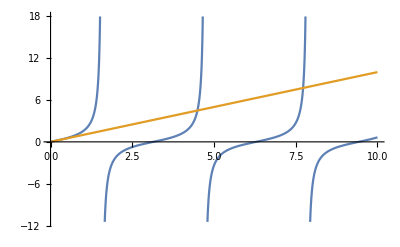

```mathematica
Plot[{Tan[x],x},{x,0,10}]
```

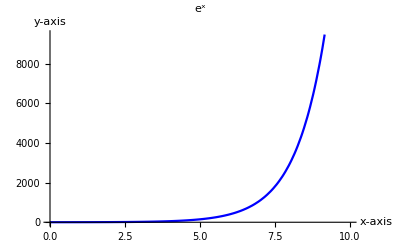

```mathematica
Plot[Exp[x],{x,0,10},PlotStyle ->{Blue},PlotLabel ->"e^x",AxesLabel->{"x-axis","y-axis"}]
```

```mathematica
1/3≥1/2
```

False

```mathematica
π≠-1
```

True

```mathematica
¬ 2==1
```

True

```mathematica
Expand[((x^2)+y^2)*(x+y)]
```

x^3+x^2 y+x y^2+y^3

```mathematica
Simplify[x^3+x^2 y+x y^2+y^3]
```

x^3+x^2 y+x y^2+y^3

```mathematica
FullSimplify[x^3+x^2 y+x y^2+y^3]
```

(x+y) (x^2+y^2)

```mathematica
Together[1/z+1/(z+1)-1/(z+2)]
```

```mathematica
(2+4 z+z^2)/(z (1+z) (2+z))
```

```mathematica
Apart[(2+4 z+z^2)/(z (1+z) (2+z))]
```

1/z+1/(1+z)-1/(2+z)

```mathematica
Solve[z^2+1==2,z]
```

{{z→-1},{z→1}}

```mathematica
z^2+1/.Rule[z,{1,-1}]
```

{2,2}

```mathematica
Information[Rule]
```

```mathematica
Solve[{x+y+z==2,6x-4y+5z==3,x+2y+2z==1},{x,y,z}]
```

{{x→3,y→10/9,z→-19/9}}

```mathematica
EQ1=x+y+z==2;EQ2=6 x-4 y+5 z==3;EQ3=x+2 y+2 z==1;
Solve[{EQ1,EQ2,EQ3},{x,y,z}]
```

{{x→3,y→10/9,z→-19/9}}

```mathematica
Solve[{x+y+z==a,6x-4y+5z==b,x+2y+2z==c},{x,y,z}]
```

{{x→2 a-c,y→1/9 (7 a-b-c),z→1/9 (-16 a+b+10 c)}}

DateObject::form: Argument TimeObject[{6,0,0.},Instant,8.] in DateObject cannot be interpreted as a date string format

TimeZoneConvert::notz: Argument America/Los Angeles in TimeZoneConvert is not a valid TimeZone specification.

DateObject::notgran: CalendarType→Julian is not a valid granularity specification for calendar Automatic.

```mathematica
Solve[EQ1&&EQ2,{x,y}]
```

{{x→1/10 (11-9 z),y→(9-z)/10}}

```mathematica
Solve[x^2+y^2==0||x-2y==1,x]
```

{{x→-ⅈ y},{x→ⅈ y},{x→1+2 y}}

```mathematica
Solve[z^-2+1==2&&z≠1,z]
```

{{z→-1}}

```mathematica
Reduce[Cos[x]==-1,x]
```

C[1]∈ℤ&&(x==-π+2 π C[1]||x==π+2 π C[1])

```mathematica
Reduce[α+β*α^2==E,α]
```

(β==0&&α==ⅇ)||(β≠0&&(α==(-1-√(1+4 ⅇ β))/(2 β)||α==(-1+√(1+4 ⅇ β))/(2 β)))

```mathematica
LinguisticAssistant   (*假装自己网不好才不出结果的，懂的都懂*)
```

Failure[…]

```mathematica
Clear[W];W:=RandomReal[];W
```

0.829921

```mathematica
W==W
```

False

```mathematica
Clear[W];W=RandomReal[];W
```

0.952328

```mathematica
W==W
```

True

```mathematica
(*  这里应该有:= 和 = 是不一样的结果*)
```

```mathematica
Timing[Power[10,100000000];]
```

{0.765625,Null}

```mathematica
Timing[10^100000000;]
```

{0.8125,Null}

```mathematica
AbsoluteTiming[10^100000000;]
```

{0.869941,Null}

```mathematica
TimeConstrained[10^100000000,0.1]
```

$Aborted

```mathematica
"Hello World" (*This is a comment*)
```

Hello World

```mathematica
ToString[23.423563]
```

23.4236

```mathematica
%//Head(*We use Head to knwo what type of objetc is*)
```

String

```mathematica
"Welcome to Mathematica"
```

Welcome to Mathematica

```mathematica
AtomQ["The sky is blue and tomorrow is expected to rain"]
```

True

```mathematica
AtomQ["Li is g"]
```

True

```mathematica
AtomQ["I am cool"]
```

True

```mathematica
Characters["Hello World"] (*Function that breaks the string into its characters*)
```

{H,e,l,l,o, ,W,o,r,l,d}

```mathematica
StringReplace["Hello this is a string ",{"h","H"}->"YourHero"]
(*This function repalce the string each time it appears for rule of the pattern,that is 4*)
```

YourHeroello tYourHerois is a string

```mathematica
StringJoin["Nice","to","have","you","back"]
```

Nicetohaveyouback

```mathematica
"Nice"<>"to"<>"have"<>"you"<>"back"
```

Nicetohaveyouback

```mathematica
StandardForm[1/x+x^2]
```

1/x+x^2

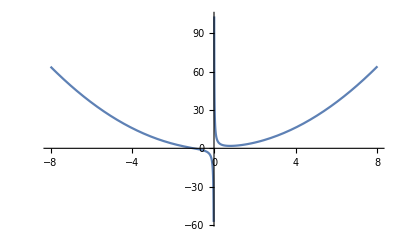

```mathematica
Plot[1/x+x^2,{x,-8,8}]
```

```mathematica
Subscript[a,x]
```

a_x

```mathematica
Trace[Plus[4,Times[Rational[1,2],t]]]
```

{{{Rational[1,2],1/2},t/2},4+t/2}